Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 8 Polar Form
Represent in polar form and graph in the complex plane as in Fig. 325.

1.  1 + I

```mathematica
Clear["Global`*"]
```

```mathematica
z=1+ⅈ
```

1+ⅈ

```mathematica
(*ComplexToPolar[z_]/;z∈Complexes:=Abs[z] Exp[ⅈ Arg[z]]*)
```

```mathematica
dd=Abs[z];ee=Arg[z];
```

```mathematica
ComplexToPolar[dd_,ee_]:=HoldForm[dd(Cos[ee]+ ⅈ Sin[ee])]
```

```mathematica
ComplexToPolar[dd,ee]
```

√2 (Cos[π/4]+ⅈ Sin[π/4])

```mathematica
PolarPlot[√2,{θ,π/4,π/(4(.999))},ImageSize->130]
```

-Graphics-

An extra plot thrown in (above) just to show something in polar coordinates.

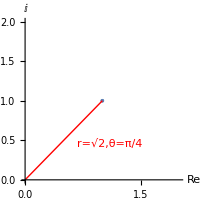

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->Automatic,ImageSize->200,AxesLabel->{Re,I},Epilog->{Red,Line[{{0,0},{1,1}}],Text["r=√2,θ=π/4",{1.1,0.45}]}]
```

I reluctantly convert away from polar coordinates to cartesian, due to a shortcoming in Mathematica plotting capabilities, or to my ignorance.

3.  2 I, -2 I

```mathematica
z=2ⅈ
```

2 ⅈ

```mathematica
dd=Abs[z];ee=Arg[z];
```

```mathematica
ComplexToPolar[dd_,ee_]:=HoldForm[dd(Cos[ee]+ ⅈ Sin[ee])]
```

```mathematica
ComplexToPolar[dd,ee]
```

2 (Cos[π/2]+ⅈ Sin[π/2])

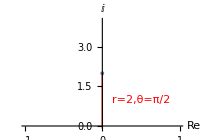

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->.7,ImageSize->200,AxesLabel->{Re,I},Epilog->{Red,Line[{{0,0},{0,2}}],Text["r=2,θ=π/2",{0.5,1}]}]
```

```mathematica
z=-2ⅈ
```

-2 ⅈ

```mathematica
dd=Abs[z];ee=Arg[z];
```

```mathematica
ComplexToPolar[dd_,ee_]:=Hold[dd(Cos[ee]+ ⅈ Sin[ee])]
```

```mathematica
ComplexToPolar[dd,ee]
```

Hold[2 (Cos[-π/2]+ⅈ Sin[-π/2])]

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->.7,ImageSize->200,AxesLabel->{Re,I},Epilog->{Red,Line[{{0,0},{0,2}}],Text["r=2,θ=π/2",{0.5,1}]}]
```

-Graphics-

5. (√2+ⅈ/3)/(-√8-2 ⅈ/3)

```mathematica
z=(√2+ⅈ/3)/(-√8-2 ⅈ/3)
```

(ⅈ/3+√2)/(-(2 ⅈ)/3-2 √2)

```mathematica
dd=Abs[z];ee=Arg[z];
```

```mathematica
ComplexToPolar[dd_,ee_]:=HoldForm[dd(Cos[ee]+ ⅈ Sin[ee])]
```

```mathematica
ComplexToPolar[dd,ee]
```

1/2 (Cos[π]+ⅈ Sin[π])

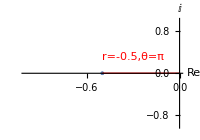

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->.7,ImageSize->200,AxesLabel->{Re,I},Epilog->{Red,Line[{{0,0},{-0.5,0}}],Text["r=-0.5,θ=π",{-0.3,0.3}]}]
```

7.  1+1/2 π ⅈ

```mathematica
z=1+1/2 π ⅈ
```

1+(ⅈ π)/2

```mathematica
dd=Abs[z];ee=Arg[z];
```

```mathematica
ComplexToPolar[dd_,ee_]:=HoldForm[dd(Cos[ee]+ ⅈ Sin[ee])]
```

```mathematica
ComplexToPolar[dd,ee]
```

√(1+π^2/4) (Cos[ArcTan[π/2]]+ⅈ Sin[ArcTan[π/2]])

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->.7,ImageSize->200,AxesLabel->{Re,I},Epilog->{Red,Line[{{0,0},{-0.5,0}}],Text["r=-0.5,θ=π",{-0.3,0.3}]}]
```

-Graphics-

9 - 14 Principal Argument
Determine the principal value of the argument and graph it as in Fig. 325.

9.  - 1 + I

In Mathematica the Arg function always returns a value between -π and π, so it is okay to just barge ahead with the calculation.

```mathematica
z=-1+ⅈ
```

-1+ⅈ

```mathematica
dd=Abs[z]
```

√2

```mathematica
ee=Arg[z]
```

(3 π)/4

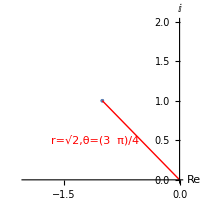

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->1,ImageSize->200,AxesLabel->{Re,I},PlotRange->Automatic,Epilog->{Red,Line[{{0,0},{-1,1}}],Text["r=√2,θ=(3  π)/4",{-1.1,0.5}]}]
```

11.  3 ± 4 I

```mathematica
z1=3+4ⅈ; z2=3-4ⅈ;
```

```mathematica
dd=Abs[z1]
```

5

```mathematica
ee=Arg[z1]
```

ArcTan[4/3]

```mathematica
dd2=Abs[z2]
```

5

```mathematica
ee2=Arg[z2]
```

-ArcTan[4/3]

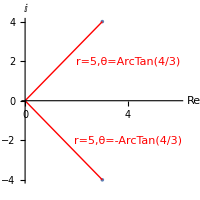

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2}}],AspectRatio->1,ImageSize->200,AxesLabel->{Re,I},PlotRange->Automatic,Epilog->{Red,Line[{{0,0},{3,4}}],Line[{{0,0},{3,-4}}],Text["r=5,θ=ArcTan(4/3)",{4,2}],Text["r=5,θ=-ArcTan(4/3)",{4,-2}]}]
```

13.  (1+ⅈ)^20

```mathematica
z=(1+ⅈ)^20
```

-1024

```mathematica
dd=Abs[z]
```

1024

```mathematica
ee=Arg[z]
```

π

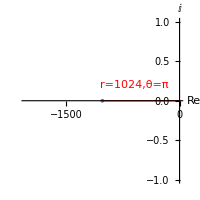

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee}}],AspectRatio->1,ImageSize->200,AxesLabel->{Re,I},PlotRange->Automatic,Epilog->{Red,Line[{{0,0},{-1024,0}}],Text["r=1024,θ=π",{-600,0.2}]}]
```

15 - 18 Conversion to x + ⅈy

15.  3 (Cos[1/2 π] -ⅈ Sin[1/2 π])

```mathematica
z=3 (Cos[1/2 π] -ⅈ Sin[1/2 π])
```

-3 ⅈ

17.  √8(Cos[1/4 π]+ⅈ Sin[1/4 π])

```mathematica
z=√8(Cos[1/4 π]+ⅈ Sin[1/4 π])
```

2+2 ⅈ

As can be seen from the two cells above, Mathematica does this section through automatic simplification.

21 - 27 Roots
Find and graph all roots in the complex plane.

21.  (1+ⅈ)^(1/3)

```mathematica
pts=({Re@#,Im@#}&/@(x/.Solve[x^3==1+ⅈ]))
```

{{Re[(1+ⅈ)^(1/3)],Im[(1+ⅈ)^(1/3)]},{Re[-(-1)^(1/3) (1+ⅈ)^(1/3)],Im[-(-1)^(1/3) (1+ⅈ)^(1/3)]},{Re[(-1)^(2/3) (1+ⅈ)^(1/3)],Im[(-1)^(2/3) (1+ⅈ)^(1/3)]}}

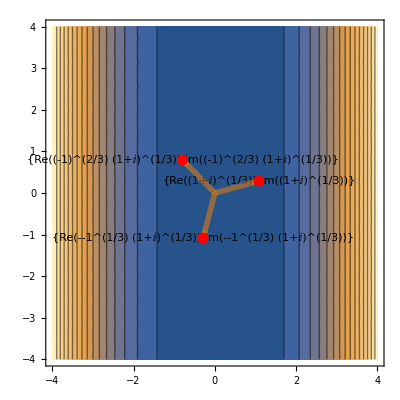

```mathematica
Show[ContourPlot[Abs[x^3-(1+ⅈ)],{x,-4,4},{y,-4,4},Contours->15],Graphics[{{Style[Text[#,#],11]&/@#},{Opacity[.5],Orange,Thickness[.01],Arrow[{{0,0},#}]&/@#},{Red,PointSize[.02],Point@#}},Axes->True,Frame->True,PlotRangePadding->1,AspectRatio->Automatic]&@pts]
```

The above sketch, which is a little confusing, applies to the answer, and its precursor can be found in the Mathematica documentation on the page “Plot Complex Roots”.

```mathematica
jj=Solve[x^3-1-ⅈ==0,x]
```

{{x→(1+ⅈ)^(1/3)},{x→-(-1)^(1/3) (1+ⅈ)^(1/3)},{x→(-1)^(2/3) (1+ⅈ)^(1/3)}}

In order to make the equation easier to work with, I cubed both sides.

```mathematica
x/.jj
```

{(1+ⅈ)^(1/3),-(-1)^(1/3) (1+ⅈ)^(1/3),(-1)^(2/3) (1+ⅈ)^(1/3)}

```mathematica
ComplexExpand[x^3-1-ⅈ/.jj]
```

{0,0,0}

The above cell demonstrates that all of Mathematica's roots work.

```mathematica
mine1=N[(1+ⅈ)^(1/3)]
```

1.08422+0.290515 ⅈ

The green cell above matches the text answer for one root, shown by answer below, ans1.

```mathematica
ans1=N[2^(1/6)(Cos[π/12]+ⅈ Sin[π/12])]
```

1.08422+0.290515 ⅈ

```mathematica
ComplexExpand[.08(1.0842150814913512+0.29051455550725136 ⅈ)^3-1-ⅈ]
```

-1.+ⅈ (-1.+1. .08)+1. .08

In the above yellow cell the text’s first answer, ans1, is proved to be a valid root.

```mathematica
mine2=N[-(-1)^(1/3) (1+ⅈ)^(1/3)]
```

-0.290515-1.08422 ⅈ

The green cell above matches a root found by the s.m. in a cyan cell, sm3, which does NOT match a text answer.

```mathematica
ans2=N[2^(1/6)(Cos[(9π)/12]+ⅈ Sin[π/12])]
```

-0.793701+0.290515 ⅈ

```mathematica
ComplexExpand[.08(-0.7937005259840997+0.29051455550725136 ⅈ)^3-1-ⅈ]
```

-1.+ⅈ (-1.+0.524519 .08)-0.299038 .08

In the above brown cell a text answer, ans2, fails to prove as root.

```mathematica
sm2=N[2^(1/6)(Cos[(9π)/12]+ⅈ Sin[(9π)/12])]
```

-0.793701+0.793701 ⅈ

```mathematica
mine3=N[(-1)^(2/3) (1+ⅈ)^(1/3)]
```

-0.793701+0.793701 ⅈ

The green cell above matches a root found by the s.m. in a cyan cell, sm2, which does NOT match a text answer.

```mathematica
ans3=N[2^(1/6)(Cos[(17π)/12]+ⅈ Sin[π/12])]
```

-0.290515+0.290515 ⅈ

```mathematica
ComplexExpand[.08(-0.2905145555072514+0.2905145555072514 ⅈ)^3-1-ⅈ]
```

-1.+ⅈ (-1.+0.0490381 .08)+0.0490381 .08

```mathematica
sm3=N[2^(1/6)(Cos[(17π)/12]+ⅈ Sin[(17π)/12])]
```

-0.290515-1.08422 ⅈ

In the above brown cell a text answer, ans3, fails to prove as root. The answers of the s.m. in this case show that the text answer omits a vital “k” factor. For example, where ‘17’ shows in two places in the cyan cell above, it applies to only one place in the text answer.

```mathematica
dd=Abs[ComplexExpand[(1+ⅈ)^(1/3)]];
```

```mathematica
ee=Arg[ComplexExpand[(1+ⅈ)^(1/3)]];
```

```mathematica
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[-(-1)^(1/3) (1+ⅈ)^(1/3)]];
```

```mathematica
ee2=Arg[ComplexExpand[ -(-1)^(1/3)(1+ⅈ)^(1/3)]];
```

```mathematica
cc2=FromPolarCoordinates[{dd2,ee2}];
```

```mathematica
dd3=Abs[ComplexExpand[(-1)^(2/3) (1+ⅈ)^(1/3)]];
```

```mathematica
cc3=FromPolarCoordinates[{dd3,ee3}];
```

```mathematica
ee3=Arg[ComplexExpand[(-1)^(2/3) (1+ⅈ)^(1/3)]];
```

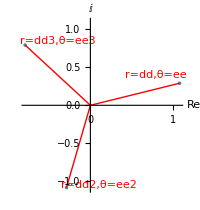

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2},{dd3,ee3}}],AspectRatio->1.05,ImageSize->200,AxesLabel->{Re,I},PlotRange->{-1.1,1.1},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{0.8,0.4}],Line[{{0,0},{cc3[[1]],cc3[[2]]}}],Text["r=dd3,θ=ee3",{-0.4,0.85}],Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{0.1,-1.05}]}]
```

The above sketch resembles the one in the s.m.

23.  216^(1/3)

```mathematica
Clear["Global`*"]
```

```mathematica
jj=Solve[x^3-216==0,x]
```

{{x→6},{x→-6 (-1)^(1/3)},{x→6 (-1)^(2/3)}}

```mathematica
x/.jj
```

{6,-6 (-1)^(1/3),6 (-1)^(2/3)}

```mathematica
ComplexExpand[x^3-216/.jj]
```

{0,0,0}

The above cell demonstrates that all of Mathematica’s roots work.

```mathematica
ComplexExpand[-6 (-1)^(1/3)]
```

-3-3 ⅈ √3

```mathematica
ComplexExpand[6 (-1)^(2/3)]
```

-3+3 ⅈ √3

The roots in the green cell above match the answer in the text.

```mathematica
dd=Abs[ComplexExpand[6]];
ee=Arg[ComplexExpand[6]];
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[-6 (-1)^(1/3)]];
ee2=Arg[ComplexExpand[-6 (-1)^(1/3)]];
cc2=FromPolarCoordinates[{dd2,ee2}];
```

```mathematica
dd3=Abs[ComplexExpand[6 (-1)^(2/3)]];
ee3=Arg[ComplexExpand[6 (-1)^(2/3)]];
cc3=FromPolarCoordinates[{dd3,ee3}];
```

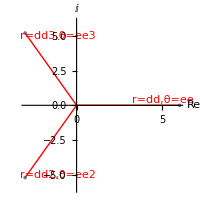

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2},{dd3,ee3}}],AspectRatio->1.05,ImageSize->200,AxesLabel->{Re,I},PlotRange->{-6,6},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{5,0.4}],Line[{{0,0},{cc3[[1]],cc3[[2]]}}],Text["r=dd3,θ=ee3",{-1.1,5}],Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{-1.1,-5}]}]
```

25.  ⅈ^(1/4)

```mathematica
Clear["Global`*"]
```

```mathematica
jj=Solve[x^4-ⅈ==0,x]
```

{{x→-(-1)^(1/8)},{x→(-1)^(1/8)},{x→-(-1)^(5/8)},{x→(-1)^(5/8)}}

```mathematica
x/.jj
```

{-(-1)^(1/8),(-1)^(1/8),-(-1)^(5/8),(-1)^(5/8)}

```mathematica
ComplexExpand[x^4-ⅈ/.jj]
```

{0,0,0,0}

The above cell demonstrates that all of Mathematica’s roots work.

```mathematica
hre[k_]=Cos[π/8+(k π)/2]+ⅈ Sin[π/8+(k π)/2]
```

```mathematica
Cos[π/8+(k π)/2]+ⅈ Sin[π/8+(k π)/2]
```

```mathematica
tab=Table[hre[k],{k,0,3}]
```

{Cos[π/8]+ⅈ Sin[π/8],ⅈ Cos[π/8]-Sin[π/8],-Cos[π/8]-ⅈ Sin[π/8],-ⅈ Cos[π/8]+Sin[π/8]}

```mathematica
Simplify[Table[ComplexExpand[k^4-ⅈ,{k,{Cos[π/8]+ⅈ Sin[π/8],ⅈ Cos[π/8]-Sin[π/8],-Cos[π/8]-ⅈ Sin[π/8],-ⅈ Cos[π/8]+Sin[π/8]}}],{k,{Cos[π/8]+ⅈ Sin[π/8],ⅈ Cos[π/8]-Sin[π/8],-Cos[π/8]-ⅈ Sin[π/8],-ⅈ Cos[π/8]+Sin[π/8]}}]]
```

{0,0,0,0}

The above cell demonstrates that all of the text’s roots work. According to the Rouché theorem there should be exactly four roots, so these roots must be the same as Mathematica's, right? To demonstrate, I will convert one of them:

```mathematica
TrigToExp[Cos[π/8]+ⅈ Sin[π/8]]
```

ⅇ^((ⅈ π)/8)

```mathematica
Simplify[%]
```

(-1)^(1/8)

On the basis of the above there is green cell above, though the format of individual answers is not exactly like the answers in the text.

```mathematica
dd=Abs[ComplexExpand[-(-1)^(1/8)]];
ee=Arg[ComplexExpand[-(-1)^(1/8)]];
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[(-1)^(1/8)]];
ee2=Arg[ComplexExpand[(-1)^(1/8)]];
cc2=FromPolarCoordinates[{dd2,ee2}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[Cos[π/8]^2+Sin[π/8]^2].

```mathematica
dd3=Abs[ComplexExpand[-(-1)^(5/8)]];
ee3=Arg[ComplexExpand[-(-1)^(5/8)]];
cc3=FromPolarCoordinates[{dd3,ee3}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[Cos[π/8]^2+Sin[π/8]^2].

```mathematica
dd4=Abs[ComplexExpand[(-1)^(5/8)]];
ee4=Arg[ComplexExpand[(-1)^(5/8)]];
cc4=FromPolarCoordinates[{dd4,ee4}];
```

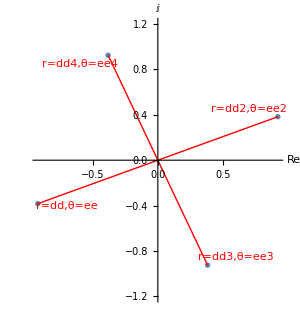

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2},{dd3,ee3},{dd4,ee4}}],AspectRatio->1.1,ImageSize->300,AxesLabel->{Re,I},PlotRange->{-1.2,1.2},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{-0.7,-0.4}],Line[{{0,0},{cc3[[1]],cc3[[2]]}}],Text["r=dd3,θ=ee3",{0.6,-0.85}],
Line[{{0,0},{cc4[[1]],cc4[[2]]}}],Text["r=dd4,θ=ee4",{-0.6,0.85}],Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{0.7,0.45}]}]
```

27.  -1^(1/5)

```mathematica
Clear["Global`*"]
```

```mathematica
jj=Solve[x^5+1==0,x]
```

{{x→-1},{x→(-1)^(1/5)},{x→-(-1)^(2/5)},{x→(-1)^(3/5)},{x→-(-1)^(4/5)}}

```mathematica
x/.jj
```

{-1,(-1)^(1/5),-(-1)^(2/5),(-1)^(3/5),-(-1)^(4/5)}

```mathematica
ComplexExpand[x^5+1/.jj]
```

{0,0,0,0,0}

The above cell demonstrates that all of Mathematica’s roots work.

```mathematica
tr1=Cos[π/5]+ⅈ Sin[π/5];
```

```mathematica
FullSimplify[ComplexExpand[tr1]]
```

```mathematica
(-1)^(1/5)  (* jj[[2]]*)
```

```mathematica
tr2=Cos[π/5]-ⅈ Sin[π/5];
```

```mathematica
FullSimplify[ComplexExpand[tr2]]
```

```mathematica
-(-1)^(4/5)  (* jj[[5]]*)
```

```mathematica
tr3=Cos[(3π)/5]-ⅈ Sin[(3π)/5];
```

```mathematica
FullSimplify[ComplexExpand[tr3]]
```

```mathematica
-(-1)^(2/5)   (* jj[[3]]*)
```

```mathematica
tr4=Cos[(3π)/5]+ⅈ Sin[(3π)/5];
```

```mathematica
FullSimplify[ComplexExpand[tr4]]
```

```mathematica
(-1)^(3/5)  (* jj[[4]]*)
```

```mathematica
tr5=-1; (* jj[[1]]*)
```

The above five tests find the text’s roots equal to Mathematica's.

```mathematica
dd=Abs[ComplexExpand[-1]];
ee=Arg[ComplexExpand[-1]];
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[(-1)^(1/5)]];
ee2=Arg[ComplexExpand[(-1)^(1/5)]];
cc2=FromPolarCoordinates[{dd2,ee2}];
```

```mathematica
dd3=Abs[ComplexExpand[-(-1)^(2/5)]];
ee3=Arg[ComplexExpand[-(-1)^(2/5)]];
cc3=FromPolarCoordinates[{dd3,ee3}];
```

```mathematica
dd4=Abs[ComplexExpand[(-1)^(3/5)]];
ee4=Arg[ComplexExpand[(-1)^(3/5)]];
cc4=FromPolarCoordinates[{dd4,ee4}];
```

```mathematica
dd5=Abs[ComplexExpand[-(-1)^(4/5)]];
ee5=Arg[ComplexExpand[-(-1)^(4/5)]];
cc5=FromPolarCoordinates[{dd5,ee5}];
```

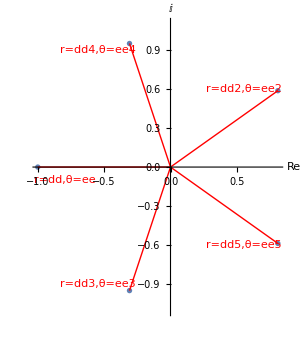

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2},{dd3,ee3},{dd4,ee4},{dd5,ee5}}],AspectRatio->1.15,ImageSize->300,AxesLabel->{Re,I},PlotRange->{-1.1,1.1},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{-0.8,-0.1}],Line[{{0,0},{cc3[[1]],cc3[[2]]}}],Text["r=dd3,θ=ee3",{-0.55,-0.9}],
Line[{{0,0},{cc4[[1]],cc4[[2]]}}],Text["r=dd4,θ=ee4",{-0.55,0.9}],
Line[{{0,0},{cc5[[1]],cc5[[2]]}}],Text["r=dd5,θ=ee5",{0.55,-0.6}],Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{0.55,0.6}]}]
```

28 - 31 Equations
Solve and graph the solutions.

29.  z^2+z+1-ⅈ==0

```mathematica
Clear["Global`*"]
```

```mathematica
jj=Solve[z^2+z+1-ⅈ==0,z]
```

{{z→-1-ⅈ},{z→ⅈ}}

```mathematica
z/.jj
```

{-1-ⅈ,ⅈ}

```mathematica
ComplexExpand[z^2+z+1-ⅈ/.jj]
```

{0,0}

The above cell demonstrates that both of Mathematica’s roots work. The green cell shows them equal to the text’s.

```mathematica
dd=Abs[ComplexExpand[-1-ⅈ]];
ee=Arg[ComplexExpand[-1-ⅈ]];
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[ⅈ]];
ee2=Arg[ComplexExpand[ⅈ]];
cc2=FromPolarCoordinates[{dd2,ee2}];
```

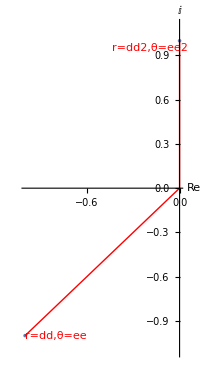

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2}}],AspectRatio->1.95,ImageSize->200,AxesLabel->{Re,I},PlotRange->{-1.1,1.1},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{-0.8,-1}],Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{-0.19,0.95}]}]
```

31.  z^4-6 ⅈ z^2+16==0

```mathematica
Clear["Global`*"]
```

```mathematica
jj=Solve[z^4-6 ⅈ z^2+16==0,z]
```

{{z→-2-2 ⅈ},{z→-1+ⅈ},{z→1-ⅈ},{z→2+2 ⅈ}}

```mathematica
z/.jj
```

{-2-2 ⅈ,-1+ⅈ,1-ⅈ,2+2 ⅈ}

```mathematica
ComplexExpand[z^4-6 ⅈ z^2+16/.jj]
```

{0,0,0,0}

The above cell demonstrates that all of Mathematica’s roots work. The green cell shows them equal to the text’s.

```mathematica
dd=Abs[ComplexExpand[-2-2 ⅈ]];
ee=Arg[ComplexExpand[-2-2 ⅈ]];
cc=FromPolarCoordinates[{dd,ee}];
```

```mathematica
dd2=Abs[ComplexExpand[-1+ⅈ]];
ee2=Arg[ComplexExpand[-1+ⅈ]];
cc2=FromPolarCoordinates[{dd2,ee2}];
```

```mathematica
dd3=Abs[ComplexExpand[1-ⅈ]];
ee3=Arg[ComplexExpand[1-ⅈ]];
cc3=FromPolarCoordinates[{dd3,ee3}];
```

```mathematica
dd4=Abs[ComplexExpand[2+2 ⅈ]];
ee4=Arg[ComplexExpand[2+2 ⅈ]];
cc4=FromPolarCoordinates[{dd4,ee4}];
```

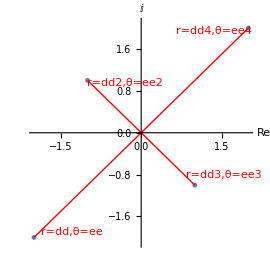

```mathematica
ListPlot[FromPolarCoordinates[{{dd,ee},{dd2,ee2},{dd3,ee3},{dd4,ee4}}],AspectRatio->1,ImageSize->270,AxesLabel->{Re,I},PlotRange->{-2.1,2.1},Epilog->{Red,Line[{{0,0},{cc[[1]],cc[[2]]}}],Text["r=dd,θ=ee",{-1.3,-1.9}],
Line[{{0,0},{cc4[[1]],cc4[[2]]}}],Text["r=dd4,θ=ee4",{1.35,1.95}],
Line[{{0,0},{cc3[[1]],cc3[[2]]}}],Text["r=dd3,θ=ee3",{1.55,-0.8}],
Line[{{0,0},{cc2[[1]],cc2[[2]]}}],Text["r=dd2,θ=ee2",{-0.3,0.95}]}]
```